SetDelayed::write: Tag List in «1» is Protected.

ReplaceAll::reps: {x[0]==2.48539} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {x[0.]==2.48539} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {x[0]==2.48539} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

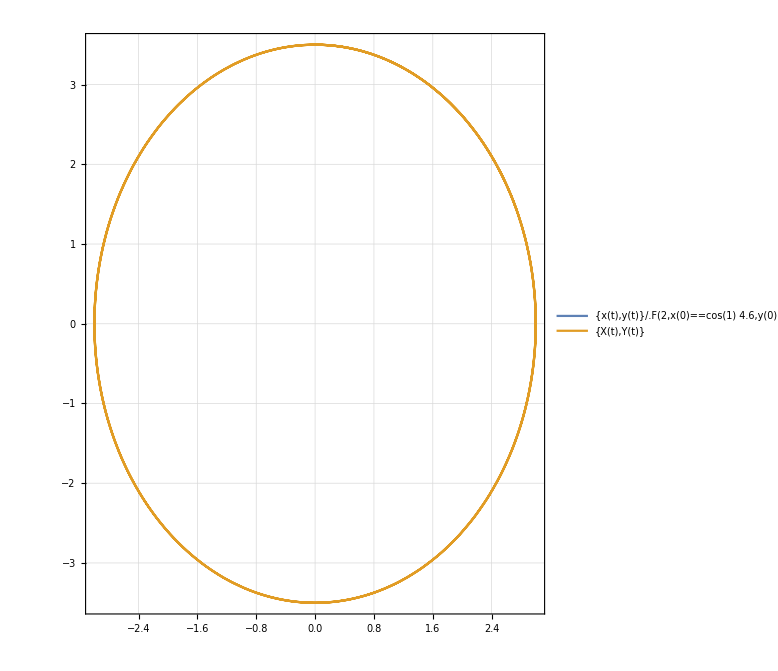

```mathematica
X[t_]:=3Sin[t];
Y[t_]:=3.5Cos[t];
F[n_,a__] := NDSolve[{(Y[t]-y[t])D[x[t],{t,n}]-(X[t]-x[t])D[y[t],{t,n}]==0, Sequence[a]}, {x,y}, {t, 0,20}];
ParametricPlot[{{x[t],y[t]}/.F[2,x[0]==Cos[1]4.6,y[0]==Sin[-1]4.6,x'[0]==Sin[1]4.6,y'[0]==Cos[1]4.6,Sqrt[y'[t]^2+x[t]^2]==4.6][[2]], {X[t],Y[t]}}, {t, 0,20},PlotTheme->"Detailed", PlotLegends->"Expressions",ImageSize->Large]
```